```mathematica
Clear["Global`*"]
```

This notebook performs evaluation of numerical and asymptotic solutions to homogenized equations of the related filtration model.
We define the governing equations, set up boundary conditions, and evaluate the solutions for different parameter values.

## Numerical solutions

#### Definitions

```mathematica
(* Homogenized system of equations *)
equations:={D[Def[x]CN'[x]-CN[x]/ϕ[x](U[x]+Def[x]ϕ'[x]),x]==f[x]CN[x],U'[x]==A/Pe ϕ[x]D[CN[x]/ϕ[x],{x,2}],Def[0]CN'[0]-CN[0]((1-A)/(ϕ[0]-A CN[0])+Def[0]/ϕ[0] ϕ'[0])==-1,CN'[1]==CN[1]/ϕ[1] ϕ'[1],U[0]==(1-A)/(1-(A CN[0])/ϕ[0])}
(* Effective coefficients *)
Def[x_]:=1/(Pe ϕ[x])(1-(2 (1-ϕ[x]))/(2-ϕ[x]-0.3058 (1-ϕ[x])^4)) (* diffusion coefficient for square lattice *)
f[x_]:=k(2π)/ϕ[x] √((1-ϕ[x])/π)
λ[x_]:=f[x]CN[x]
```

#### Diffusion coefficient from cell problem

```mathematica
(* Ball radius as a function of porosity *)
R:=Sqrt[(1-phi)/Pi]
(* Definition of the unit cell *)
omega=RegionDifference[Rectangle[{-0.5,-0.5},{0.5,0.5}],Disk[{0,0},R]];
(* Closed-form diffusion coefficient for comparison *)
Dapprox[ϕ_]:=1/(Pe ϕ)(1-(2 (1-ϕ))/(2-ϕ-0.3058 (1-ϕ)^4))
```

```mathematica
(* Uploading numerical results from FlexPDE *)
Dresults={};
For[phi=0.22,phi≤1,phi+=0.015,
Data=Get["C:\\Users\\vojta\\OneDrive\\Skola\\ING\\Diplomka\\flexPDE\\Results\\CellProblemTable_"<>ToString[1000 phi]<>"txt"];
(* Calculation of the diffusion coefficient *)
gammaXFlexPDE=Interpolation[Data];
Jgamma11FlexPDE=D[gammaXFlexPDE[x,y],x];
intGamma=NIntegrate[Jgamma11FlexPDE,{x,y}∈omega];
Dfin=1-1/phi intGamma;
AppendTo[Dresults,{phi,Dfin}];]
```

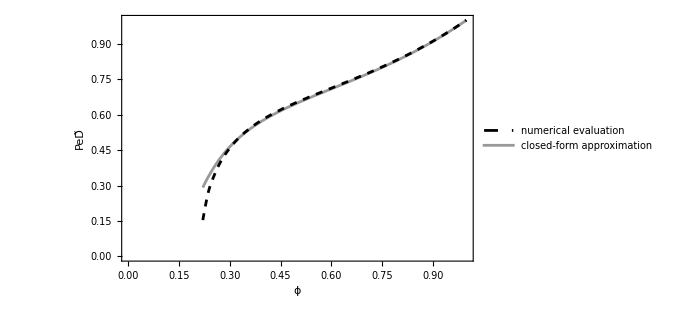

```mathematica
(* Plot of the obtained results *)
line=2;font1=21;font2=19; gray=GrayLevel[0.6];
Dplot=Plot[Pe Dapprox[x],{x,0.22,1},PlotRange->{{0,1},{0,1}},PlotStyle->{gray,AbsoluteThickness[line]}];
Dplotnum=ListPlot[Dresults,PlotStyle->{Black,Dashed,AbsoluteThickness[line]},Joined->True,InterpolationOrder->2];
graph=Show[Dplot,Dplotnum,Frame->True,FrameLabel->{Style["ϕ",FontFamily->"Times",FontSize->font1],Style[Row[{"Pe",Overscript["D","~"]}],Italic,FontFamily->"Times",FontSize->font1]},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
figure=Legended[graph,Placed[LineLegend[{Directive[Dashed,AbsoluteThickness[line]],Directive[gray,AbsoluteThickness[line]]},{"numerical evaluation","closed-form approximation"},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->Thin,FrameMargins->0]&)],{Right,Bottom}]]
```

#### Evaluation of C, U, λ

```mathematica
(* Initial set of porosity profile and parameters *)
ϕ[x_]:=0.75+m(x-0.5)
paref={A->0.6,Pe->3,k->1};

(* Calculation of numerical solutions *)
sol1=NDSolve[equations/.m->-0.3/.paref,{CN,U},{x,0,1}];
sol2=NDSolve[equations/.m->0/.paref,{CN,U},{x,0,1}];
sol3=NDSolve[equations/.m->0.3/.paref,{CN,U},{x,0,1}];
```

```mathematica
(* Evaluation of the obtained solutions *)
dashed=Dashing[{0.02,0.01}];line=2;font1=21;font2=19;
c1=Plot[Evaluate[CN[x]/. sol1],{x,0,1},PlotRange->{{0,1},{0,0.9}},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
c2=Plot[Evaluate[CN[x]/. sol2],{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];
c3=Plot[Evaluate[CN[x]/. sol3],{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];

u1=Plot[Evaluate[U[x]/. sol1],{x,0,1},PlotRange->{{0,1},{0.7,1.2}},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
u2=Plot[Evaluate[U[x]/. sol2],{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];
u3=Plot[Evaluate[U[x]/. sol3],{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];

lambda1=Plot[λ[x]/.m->-0.3/.k->1/.sol1,{x,0,1},PlotRange->{{0,1},{0,2.5}},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
lambda2=Plot[λ[x]/.m->0/.k->1/.sol2,{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];
lambda3=Plot[λ[x]/.m->0.3/.k->1/.sol3,{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];
```

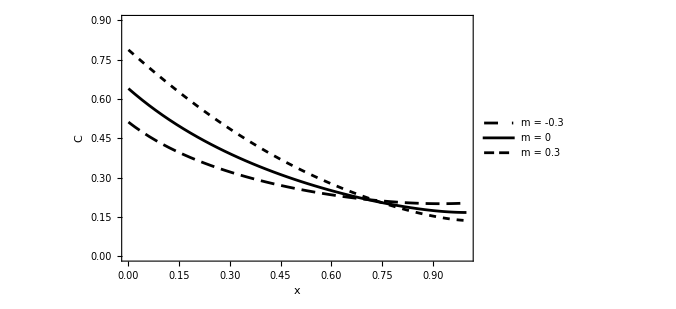

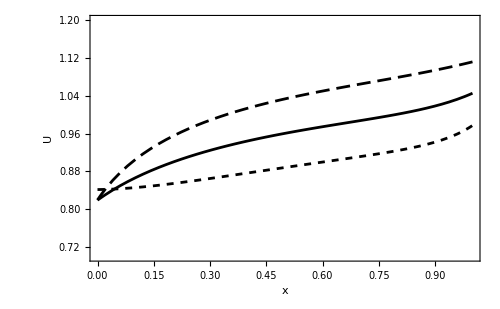

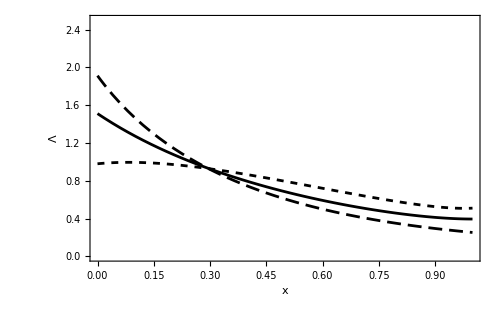

```mathematica
(* Plots of the obtained results *)
graph1=Show[c1,c2,c3,Frame->True,
FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["C",Italic,FontFamily->"Times",FontSize->font1]},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
graph2=Show[u1,u2,u3,Frame->True,
FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["U",Italic,FontFamily->"Times",FontSize->font1]},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
graph3=Show[lambda1,lambda2,lambda3,Frame->True,FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["\[\CapitalLambda]",Italic,FontFamily->"Times",
FontSize->font1]},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];

figure1=Legended[
Legended[graph1,Placed[LineLegend[{Directive[Dashed,AbsoluteThickness[line]],Directive[Black,AbsoluteThickness[line]],Directive[dashed,AbsoluteThickness[line]]},{Row[{Style["m",Italic]," = -0.3"}],Row[{Style["m",Italic]," = 0"}],Row[{Style["m",Italic]," = 0.3"}]},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->Thin,FrameMargins->0]&)],{Right,Top}]],
Placed[Style["(a)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
figure2=Legended[
graph2,
Placed[Style["(b)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
figure3=Legended[
graph3,
Placed[Style["(c)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
```

#### Evaluation of C for varying A

```mathematica
(* Initial set of porosity profile and parameters *)
ϕ[x_]:=0.75+m(x-0.5)
mset1=-0.3;mset2=0.3;
paref1={A->0.6,Pe->3,k->1};paref2={A->0 ,Pe->3,k->1};

(* Calculation of numerical solutions *)
sol4=NDSolve[equations/.m->mset1/.paref1,{CN,U},{x,0,1}];
sol5=NDSolve[equations/.m->mset1/.paref2,{CN,U},{x,0,1}];
sol6=NDSolve[equations/.m->mset2/.paref1,{CN,U},{x,0,1}];
sol7=NDSolve[equations/.m->mset2/.paref2,{CN,U},{x,0,1}];
```

```mathematica
(* Evaluation of the obtained solutions *)
line=2;font1=21;font2=19;
c4=Plot[Evaluate[CN[x]/. sol4],{x,0,1},PlotRange->{{0,0.98},{0,0.9}},PlotStyle->{Black,Dashed,AbsoluteThickness[line]},
PlotLabels->Placed[{Style[Row[{Style["m",Italic]," = -0.3"}],FontFamily->"Times",FontSize->font2]},{0.1,0.82}]];
c5=Plot[Evaluate[CN[x]/. sol5],{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];
c6=Plot[Evaluate[CN[x]/. sol6],{x,0,1},PlotStyle->{Black,Dashed,AbsoluteThickness[line]},
PlotLabels->Placed[{Style[Row[{Style["m",Italic]," = 0.3"}],FontFamily->"Times",FontSize->font2]},{0.117,0.35}]];
c7=Plot[Evaluate[CN[x]/. sol7],{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];
```

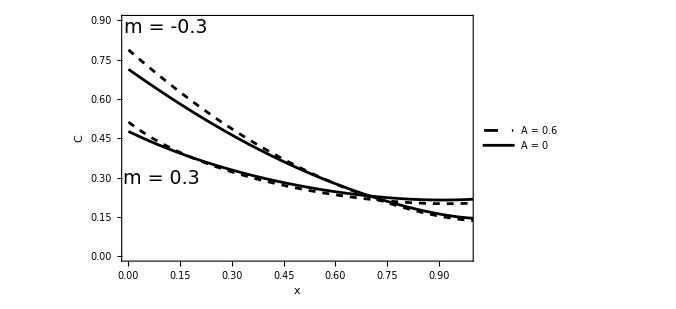

```mathematica
(* Plot of the obtained results *)
graph4=Show[c4,c5,c6,c7,Frame->True,FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["C",Italic,FontFamily->"Times",FontSize->font1]},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
figure4=Legended[graph4,Placed[LineLegend[{Directive[Dashed,AbsoluteThickness[line]],Directive[Black,AbsoluteThickness[line]]},{Row[{Style["A",Italic]," = 0.6"}],Row[{Style["A",Italic]," = 0"}]},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->Thin,FrameMargins->0]&)],{Right,Top}]]
```

#### Comparison of Square vs Hexagonal lattice

```mathematica
(* Initial set of porosity profile and parameters *)
ϕ[x_]:=0.75+m(x-0.5)
mset1=-0.3;mset2=0.3;
paref={A->0.6 ,Pe->3,k->1};

(* Effective coefficients for hexagonal lattice *)
Def[x_]:=1/(Pe ϕ[x])(1-(2 (1-ϕ[x]))/(2-ϕ[x]-0.07542 (1-ϕ[x])^6))
f[x_]:=k(4π)/ϕ[x] √((1-ϕ[x])/(2π))

(* Calculation of numerical solutions *)
sol10=NDSolve[equations/.m->mset1/.paref,{CN,U},{x,0,1}];
sol11=NDSolve[equations/.m->mset2/.paref,{CN,U},{x,0,1}];
```

```mathematica
(* Evaluation of the obtained solutions *)
line=2.5;font1=23;font2=21; gray=GrayLevel[0.6];
c10=Plot[Evaluate[CN[x]/. sol10],{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];
c11=Plot[Evaluate[CN[x]/. sol11],{x,0,1},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
lambda6=Plot[λ[x]/.m->mset1/.k->1/.sol10,{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];
lambda7=Plot[λ[x]/.m->mset2/.k->1/.sol11,{x,0,1},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
```

```mathematica
(* Effective coefficients for square lattice *)
f[x_]:=k(2π)/ϕ[x] √((1-ϕ[x])/π)
Def[x_]:=1/(Pe ϕ[x])(1-(2 (1-ϕ[x]))/(2-ϕ[x]-0.3058 (1-ϕ[x])^4))

(* Calculation of numerical solutions *)
sol8=NDSolve[equations/.m->mset1/.paref,{CN,U},{x,0,1}];
sol9=NDSolve[equations/.m->mset2/.paref,{CN,U},{x,0,1}];
```

```mathematica
(* Evaluation of the obtained solutions *)
c8=Plot[Evaluate[CN[x]/. sol8],{x,0,1},PlotRange->{{0,1},{0,0.9}},PlotStyle->{gray,dashed,AbsoluteThickness[line]}];
c9=Plot[Evaluate[CN[x]/. sol9],{x,0,1},PlotStyle->{gray,Dashed,AbsoluteThickness[line]}];
lambda4=Plot[λ[x]/.m->mset1/.k->1/.sol8,{x,0,1},PlotRange->{{0,1},{0,2.6}},PlotStyle->{gray,dashed,AbsoluteThickness[line]}];
lambda5=Plot[λ[x]/.m->mset2/.k->1/.sol9,{x,0,1},PlotStyle->{gray,Dashed,AbsoluteThickness[line]}];
```

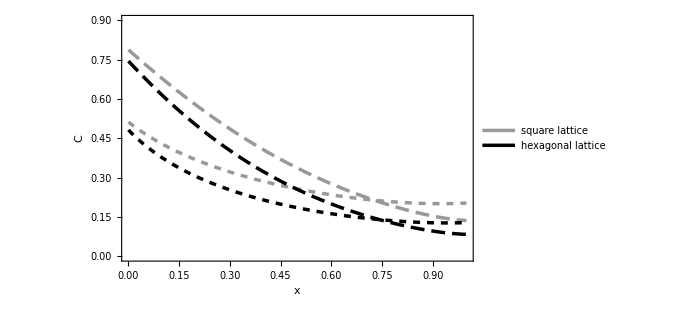

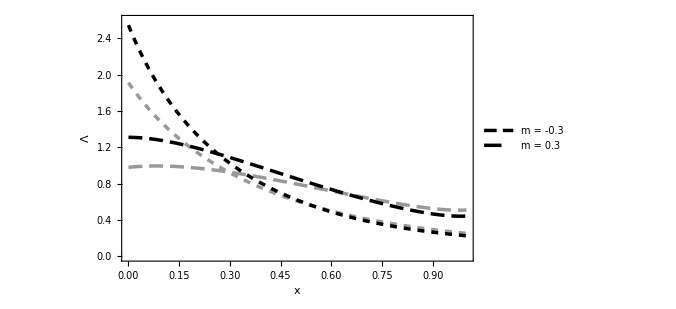

```mathematica
(* Plots of the obtained results *)
graph5=Show[c8,c9,c10,c11,Frame->True,FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["C",Italic,FontFamily->"Times",FontSize->font1]},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
graph6=Show[lambda4,lambda5,lambda6,lambda7,Frame->True,FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["\[\CapitalLambda]",Italic,FontFamily->"Times",
FontSize->font1]},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];

figure5=Legended[
Legended[graph5,Placed[LineLegend[{Directive[gray,AbsoluteThickness[line]],Directive[Black,AbsoluteThickness[line]]},{"square lattice","hexagonal lattice"},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->Thin,FrameMargins->0]&)],{Right,Top}]],
Placed[Style["(a)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
figure6=Legended[
Legended[graph6,Placed[LineLegend[{Directive[dashed,AbsoluteThickness[line]],Directive[Dashed,AbsoluteThickness[line]]},{Row[{Style["m",Italic]," = -0.3"}],Row[{Style["m",Italic]," = 0.3"}]},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->Thin,FrameMargins->0]&)],{Right,Top}]],
Placed[Style["(b)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
```

#### Evaluation of efficiency metrics T, S

```mathematica
(* Initial set of parameters *)
paref={A->0.6 ,Pe->3,k->1};
```

```mathematica
(* Calculation of discrete values for mean porosity 0.7 *)
T0p70={};S0p70={};NumPoints=80;
ϕ[x_]:=0.7+m(x-0.5);
For[mm=-0.38,mm≤0.38,mm+=0.76/(NumPoints-1),
sol=NDSolve[equations/.m->mm/.paref,CN,{x,0,1}];Tmm=NIntegrate[λ[x]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [T0p70,{mm,Tmm[[1]]}];Smm=NIntegrate[Abs[λ[x]-Tmm[[1]]]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [S0p70,{mm,Smm[[1]]}];]
```

```mathematica
(* Calculation of discrete values for mean porosity 0.75 *)
T0p75={};S0p75={};NumPoints=100;
ϕ[x_]:=0.75+m(x-0.5);
For[mm=-0.48,mm≤0.48,mm+=0.96/(NumPoints-1),
sol=NDSolve[equations/.m->mm/.paref,CN,{x,0,1}];Tmm=NIntegrate[λ[x]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [T0p75,{mm,Tmm[[1]]}];Smm=NIntegrate[Abs[λ[x]-Tmm[[1]]]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [S0p75,{mm,Smm[[1]]}];]
```

```mathematica
(* Calculation of discrete values for mean porosity 0.8 *)
T0p80={};S0p80={};NumPoints=80;
ϕ[x_]:=0.8+m(x-0.5);
For[mm=-0.38,mm≤0.38,mm+=0.76/(NumPoints-1),
sol=NDSolve[equations/.m->mm/.paref,CN,{x,0,1}];Tmm=NIntegrate[λ[x]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [T0p80,{mm,Tmm[[1]]}];Smm=NIntegrate[Abs[λ[x]-Tmm[[1]]]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [S0p80,{mm,Smm[[1]]}];]
```

```mathematica
(* Calculation of discrete values for mean porosity 0.85 *)
T0p85={};S0p85={};NumPoints=60;
ϕ[x_]:=0.85+m(x-0.5);
For[mm=-0.28,mm≤0.28,mm+=0.56/(NumPoints-1),
sol=NDSolve[equations/.m->mm/.paref,CN,{x,0,1}];Tmm=NIntegrate[λ[x]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [T0p85,{mm,Tmm[[1]]}];Smm=NIntegrate[Abs[λ[x]-Tmm[[1]]]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [S0p85,{mm,Smm[[1]]}];]
```

```mathematica
(* Calculation of discrete values for mean porosity 0.9 *)
T0p90={};S0p90={};NumPoints=40;
ϕ[x_]:=0.9+m(x-0.5);
For[mm=-0.18,mm≤0.18,mm+=0.36/(NumPoints-1),
sol=NDSolve[equations/.m->mm/.paref,CN,{x,0,1}];Tmm=NIntegrate[λ[x]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [T0p90,{mm,Tmm[[1]]}];Smm=NIntegrate[Abs[λ[x]-Tmm[[1]]]/.m->mm/.k->1/.sol,{x,0,1}];AppendTo [S0p90,{mm,Smm[[1]]}];]
```

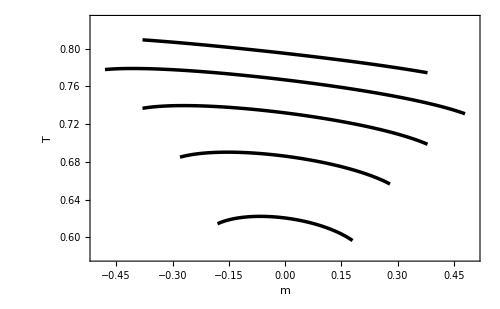

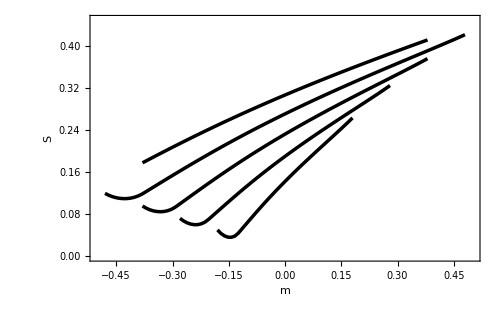

```mathematica
(* Plots of the obtained results *)
line=2.5;font1=23;font2=21;
graph7=ListPlot[{T0p70,T0p75,T0p80,T0p85,T0p90},Joined->True,PlotRange->{{-0.5,0.5},{0.58,0.83}},PlotStyle->{Directive[Black,AbsoluteThickness[line]]},Frame->True,FrameLabel->{{Rotate[Style["T",Italic,FontFamily->"Times",FontSize->font1],-Pi/2],None},{Style["m",Italic,FontFamily->"Times",FontSize->font1],None}},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
graph8=ListPlot[{S0p70,S0p75,S0p80,S0p85,S0p90},Joined->True,PlotRange->{{-0.5,0.5},{0,0.45}},PlotStyle->{Directive[Black,AbsoluteThickness[line]]},Frame->True,Axes->False,FrameLabel->{{Rotate[Style["S",Italic,FontFamily->"Times",FontSize->font1],-Pi/2],None},{Style["m",Italic,FontFamily->"Times",FontSize->font1],None}},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500];
figure7=Legended[
graph7,
Placed[Style["(a)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
figure8=Legended[
graph8,
Placed[Style["(b)",FontFamily->"Times",FontSize->font1],{Left,Above}]]
```

## Asymptotic solutions

#### Definitions

```mathematica
(* Leading-order solution *)
C0[x_]:=2 α ϕ0 Exp[a x] (b Cosh[a b (1-x)]+Sinh[a b (1-x)])

(* Definition of parameters *)
aset=1/(2 ϕ0 D0);bset=√(1+f0/(D0 aset^2));αset=1/((bset^2+1)Sinh[aset bset]+2 bset Cosh[aset bset]);θset=A1 (2 αset Sinh[aset bset] (1-ϕ0/Pe aset (1-bset^2))+2 αset bset Cosh[aset bset]-1);
parab={a->aset,b-> bset,α-> αset,θ->θset};

(* First-order solutions *)
C1[x_]:=Exp[a x] ((α1[x]+αt1) Exp[a b x]+(α2[x]+αt2) Exp[-a b x])
U1[x_]:=(A1 C0'[x])/Pe+θ
α1[x_]:=1/(2 a b D0)∫G[x] Exp[-(1+b) a x]ⅆx
α2[x_]:=-1/(2 a b D0)∫G[x] Exp[-(1-b) a x]ⅆx
n[x_]:=D1[x] C0'[x]-C0[x]/ϕ0(U1[x]+D0 ϕ1'[x]-ϕ1[x]/ϕ0)
G[x_]:=-n'[x]+f1[x] C0[x]

(* Leading-order effective coefficients *)
D0set=1/(Pe ϕ0)(1-(2(1- ϕ0))/(2-ϕ0-0.3058 (1-ϕ0)^4));
f0set= k(2π)/ϕ0 √((1-ϕ0)/π);
parDf={D0->D0set,f0->f0set};

(* First-order effective coefficients *)
D1[x_]:=ϕ1[x] D[1/(Pe ϕ)(1-(2 (1-ϕ))/(2-ϕ-0.3058 (1-ϕ)^4)),ϕ]/.ϕ->ϕ0
f1[x_]:=ϕ1[x] k(ϕ0-2)/ϕ0^2 √(π/(1-ϕ0))
```

#### Evaluation

```mathematica
(* Initial set of porosity profile *)
ϕ0=0.75;
ϕ1[x_]:=x-0.5
ϕ[x_]:=ϕ0+m ϕ1[x];

(* Pre-calculation of solution parameters *)
α10=α1[x]/.x->0//Simplify;
α11=α1[x]/.x->1//Simplify;
α20=α2[x]/.x->0//Simplify;
α21=α2[x]/.x->1//Simplify;
αt2set=1/2 α (-(b^2-1) Exp[a b] (α11-α10)-(b+1)^2 Exp[a b] α20+(b-1)^2 Exp[-a b] α21+(2 α b (b-1))/a ϕ1'[1]+2 (b+1) ϕ0 Exp[a b] n[0]);
αt1set=(b+1)/(b-1)(αt2set+α20)-α10-(2 ϕ0)/(b-1) n[0];
paralfa={αt1->αt1set,αt2->αt2set};
```

```mathematica
(* Initial set of filter parameters *)
mset1=-0.3;mset2=-0.1;
paref1={A->0.6,A1->0.6/mset1,Pe->3,k->1};
paref2={A->0.6,A1->0.6/mset2,Pe->3,k->1};

(* Calculation of numerical solutions for comparison *)
sol12=NDSolve[equations/.m->mset1/.paref1,{CN,U},{x,0,1}];
sol13=NDSolve[equations/.m->mset2/.paref2,{CN,U},{x,0,1}];
(* Evaluation of asymptotic solutions *)
c0set1=C0[x]/.parab/.parDf/.paref1//Simplify;
c1set1=C1[x]/.paralfa/.parab/.parDf/.paref1//Simplify;
c0set2=C0[x]/.parab/.parDf/.paref2//Simplify;
c1set2=C1[x]/.paralfa/.parab/.parDf/.paref2//Simplify;
```

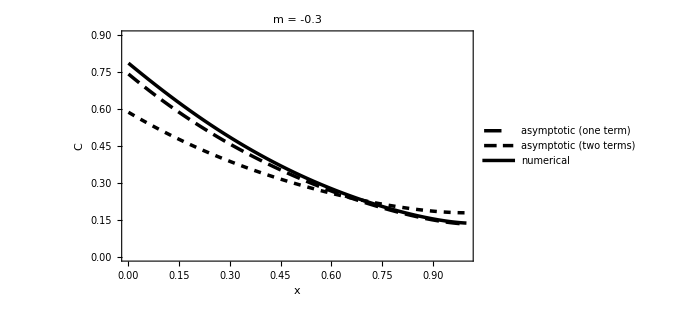

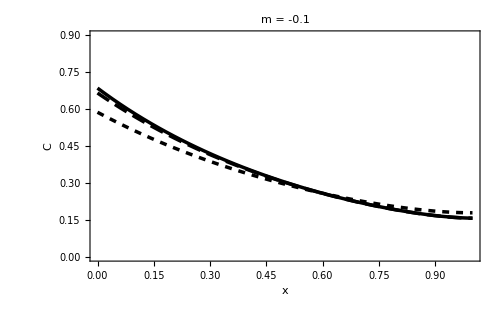

```mathematica
(* Plots of the obtained solutions *)
line=2.5;font1=23;font2=21;
c12=Plot[Evaluate[CN[x]/. sol12],{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];
c13=Plot[Evaluate[CN[x]/. sol13],{x,0,1},PlotStyle->{Black,AbsoluteThickness[line]}];

c0asym1=Plot[c0set1,{x,0,1},PlotRange->{{0,1},{0,0.9}},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
c1asym1=Plot[c0set1+mset1 c1set1,{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];
c0asym2=Plot[c0set2,{x,0,1},PlotRange->{{0,1},{0,0.9}},PlotStyle->{Black,Dashed,AbsoluteThickness[line]}];
c1asym2=Plot[c0set2+mset2 c1set2,{x,0,1},PlotStyle->{Black,dashed,AbsoluteThickness[line]}];

graph9=Show[c0asym1,c1asym1,c12,Frame->True,
FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["C",Italic,FontFamily->"Times",FontSize->font1]},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500,PlotLabel->Row[{Style["m",Italic]," = -0.3"}]];
graph10=Show[c0asym2,c1asym2,c13,Frame->True,
FrameLabel->{Style["x",Italic,FontFamily->"Times",FontSize->font1],Style["C",Italic,FontFamily->"Times",FontSize->font1]},
LabelStyle->{Black,FontFamily->"Times",FontSize->font2},RotateLabel->False,ImageSize->500,PlotLabel->Row[{Style["m",Italic]," = -0.1"}]];
figure9=Legended[
Legended[graph9,Placed[LineLegend[{Directive[Dashed,AbsoluteThickness[line]],Directive[dashed,AbsoluteThickness[line]],Directive[Black,AbsoluteThickness[line]]},{"asymptotic (one term)","asymptotic (two terms)","numerical"},LabelStyle->{Black,FontFamily->"Times",FontSize->font2},LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->Thin,FrameMargins->0]&)],{Right,Top}]],
Placed[Style["(a)",FontFamily->"Times",FontSize->font1],{Before,Top}]]
figure10=Legended[
graph10,
Placed[Style["(b)",FontFamily->"Times",FontSize->font1],{Before,Top}]]
```